## Functions

```mathematica
ReplaceDiagonal[m_]:=Module[{mat=m},Scan[(mat[[Sequence@@#]]=0)&,Table[{i,i},{i,Length@m}]];mat];
originalColorsValues={{70,50,0,0},{0,100,0,0},{0,0,0,0},{100,100,100,100},{0,0,0,0}};
colorPalette=CMYKColor[#[[1]]/100,#[[2]]/100,#[[3]]/100,#[[4]]/100]&/@originalColorsValues;
hexToRGB=RGBColor@@(IntegerDigits[ToExpression@StringReplace[#,"#"->"16^^"],256,3]/255.)&;
MapProcess[freqs_, pops_, latLon_,max_,countryName_,surv_,over_]:=Module[{
scA=10000,scB=35000, scC=.00075, cA="#1e59fc", cB="#ff007f",cC="#7737d6"
},
GeoGraphics[{
GeoStyling[EdgeForm[Directive[Opacity[.1],Thickness[.05],Darker[colorPalette[[5]],.06]]],Opacity[0],colorPalette[[1]]],
CountryData[countryName,"SchematicPolygon"],
GeoStyling[EdgeForm[Directive[Opacity[0],Thickness[.1],colorPalette[[5]]]],Opacity[0],colorPalette[[3]]],
CountryData[countryName,"SchematicPolygon"],
GeoStyling[EdgeForm[Directive[Opacity[.1],Thickness[.02],colorPalette[[2]]]],Opacity[0],colorPalette[[5]]],
CountryData[countryName,"Polygon"]
}
,AspectRatio->Automatic
,Axes->False
,Frame->True
,FrameStyle->Directive[colorPalette[[4]],Thickness[.0035]]
,FrameTicks->None
,FrameTicksStyle->Black
,GridLines->Automatic
,GridLinesStyle->Directive[{Dashed,Opacity[.25],Thickness[.001],Black}]
,ImageSize->1500
,GeoBackground->None
(*,GeoBackground->GeoStyling["ReliefMap"]
,GeoServer->"DigitalGlobe"*)
,PlotRange->{{6.6,6.75},{0.25,.4}}
,Epilog->{
(*Centrality*)
Lighter[hexToRGB[cA],.25],Opacity[.25],EdgeForm[Directive[Thickness[.002],Dashing[1],Opacity[1],hexToRGB[cA]]],
Disk[#[[1]],#[[2]]+scC]&/@Transpose[{Reverse/@latLon,(scA*(pops/Max[pops]/scB)*(freqs/max/scB))^(1/2)}],
(*Surveillance*)
hexToRGB[cB],Opacity[0.2],EdgeForm[Directive[Thickness[.002],Dashing[1],Opacity[1],hexToRGB[cB]]],
Disk[#[[1]],#[[2]]+scC]&/@Transpose[{Reverse/@(latLon[[#]]&/@surv),(scA*((pops[[#]]&/@surv)/Max[pops]/scB)*((freqs[[#]]&/@surv)/max/scB))^(1/2)}],
(*Overrun*)
hexToRGB[cB],Opacity[0.1],EdgeForm[Directive[Thickness[.002],Dashing[1],Opacity[1],hexToRGB[cC]]],
Disk[#[[1]],#[[2]]+scC]&/@Transpose[{Reverse/@(latLon[[#]]&/@over),(scA*((pops[[#]]&/@over)/Max[pops]/scB)*((freqs[[#]]&/@over)/max/scB))^(1/2)}],
(*PopSize*)
Darker[hexToRGB[cA],0],Opacity[0],EdgeForm[Directive[Thickness[.003],Dashing[.0025],Opacity[.05],Darker[hexToRGB[cA],.1]]],
Disk[#[[1]],#[[2]]+scC]&/@Transpose[{Reverse/@latLon,(pops/Max[pops]/scB)^(1/2)}]
}
]
];
HistProcess[steps_,migration_,max_]:=Module[{},
Histogram[steps,migration//Length
,AspectRatio->.1
,Axes->False
,ChartStyle->Directive[{EdgeForm[Directive[{hexToRGB["#80A1FC"],Opacity[0],Thick}]],Opacity[.5],hexToRGB["#80A1FC"]}]
,Frame->True
,FrameStyle->Directive[colorPalette[[4]],Thickness[.0035]]
,FrameTicks->None
,ImageSize->1500
,PlotRange->{{0,migration//Length},{0,max}}
]
]
```

## Load Data

```mathematica
SetDirectory[NotebookDirectory[]];
bPath= "./kernels_cluster/";
lonLatPop=Import[bPath<>"stp_cluster_sites_pop.csv"][[2;;All]];
migration=Import[bPath<>"kernel_cluster_2500_2.csv"];
(**)
latLon=Reverse/@lonLatPop[[All,1;;2]];
pops=Log[lonLatPop[[All,3]]]//N;
```

## Markov Process

```mathematica
{sp,rep}={500,2000};
(*Simulate*)
initialState=ConstantArray[0,migration//Length]//ReplacePart[#,258->1]&;
markov=DiscreteMarkovProcess[initialState,migration];
MarkovProcessProperties[markov,"LimitTransitionMatrix"][[1]];
simTraces=(RandomFunction[markov,{0,sp},rep]//Normal);
steps=#[[All,2]]&/@simTraces;
{max,maxTwo}={Tally[steps//Flatten][[All,2]]//Max,Tally[steps//Flatten][[All,2]]//Max};
```

## Export Ring

```mathematica
Table[
freqs=Count[steps[[All,1;;t]]//Flatten,#]&/@Range[1,Length[migration]];
topFreq=(freqs//Sort//Reverse)[[1;;20]];
(*surv=Position[freqs,#]&/@topFreq//Flatten;*)
over=Position[freqs,x_/;1500<x]//Flatten;
surv=Position[freqs,x_/;300<x<1500]//Flatten;
(*Map*)
countryName="São Tomé and Príncipe";
map=MapProcess[freqs, pops, latLon,max,countryName,surv,over];
hst=HistProcess[steps[[All,1;;t]]//Flatten,migration,maxTwo];
out=map;(*Grid[{{hst},{map}}];*)
(**)
Export["./img/map"<>StringPadLeft[t//ToString,4,"0"]<>".png",out]
,{t,sp}]
```

$Aborted

## Export Static

```mathematica
{tts,sites}={120,20};
Table[
freqs=Count[steps[[All,1;;t]]//Flatten,#]&/@Range[1,Length[migration]];
topFreq=(freqs//Sort//Reverse)[[1;;20]];
(**)
freqsB=Count[steps[[All,1;;tts]]//Flatten,#]&/@Range[1,Length[migration]];
topFreqB=(freqs//Sort//Reverse)[[1;;sites]];
surv=Position[freqsB,x_/;750<x<1500]//Flatten;
(*Map*);
over=Position[freqs,x_/;1500<x]//Flatten;
countryName="São Tomé and Príncipe";
map=MapProcess[freqs, pops, latLon,max,countryName,surv,over];
hst=HistProcess[steps[[All,1;;t]]//Flatten,migration,maxTwo];
out=map(*Grid[{{hst},{map}}];*);
(**)
Export["./img/map"<>StringPadLeft[t//ToString,4,"0"]<>".png",out]
,{t,sp}]
```

$Aborted

{62,69,102,110,164,165,166,168,169,170,200,202,204,206,207,209,244,246,247,249,250,252,254}

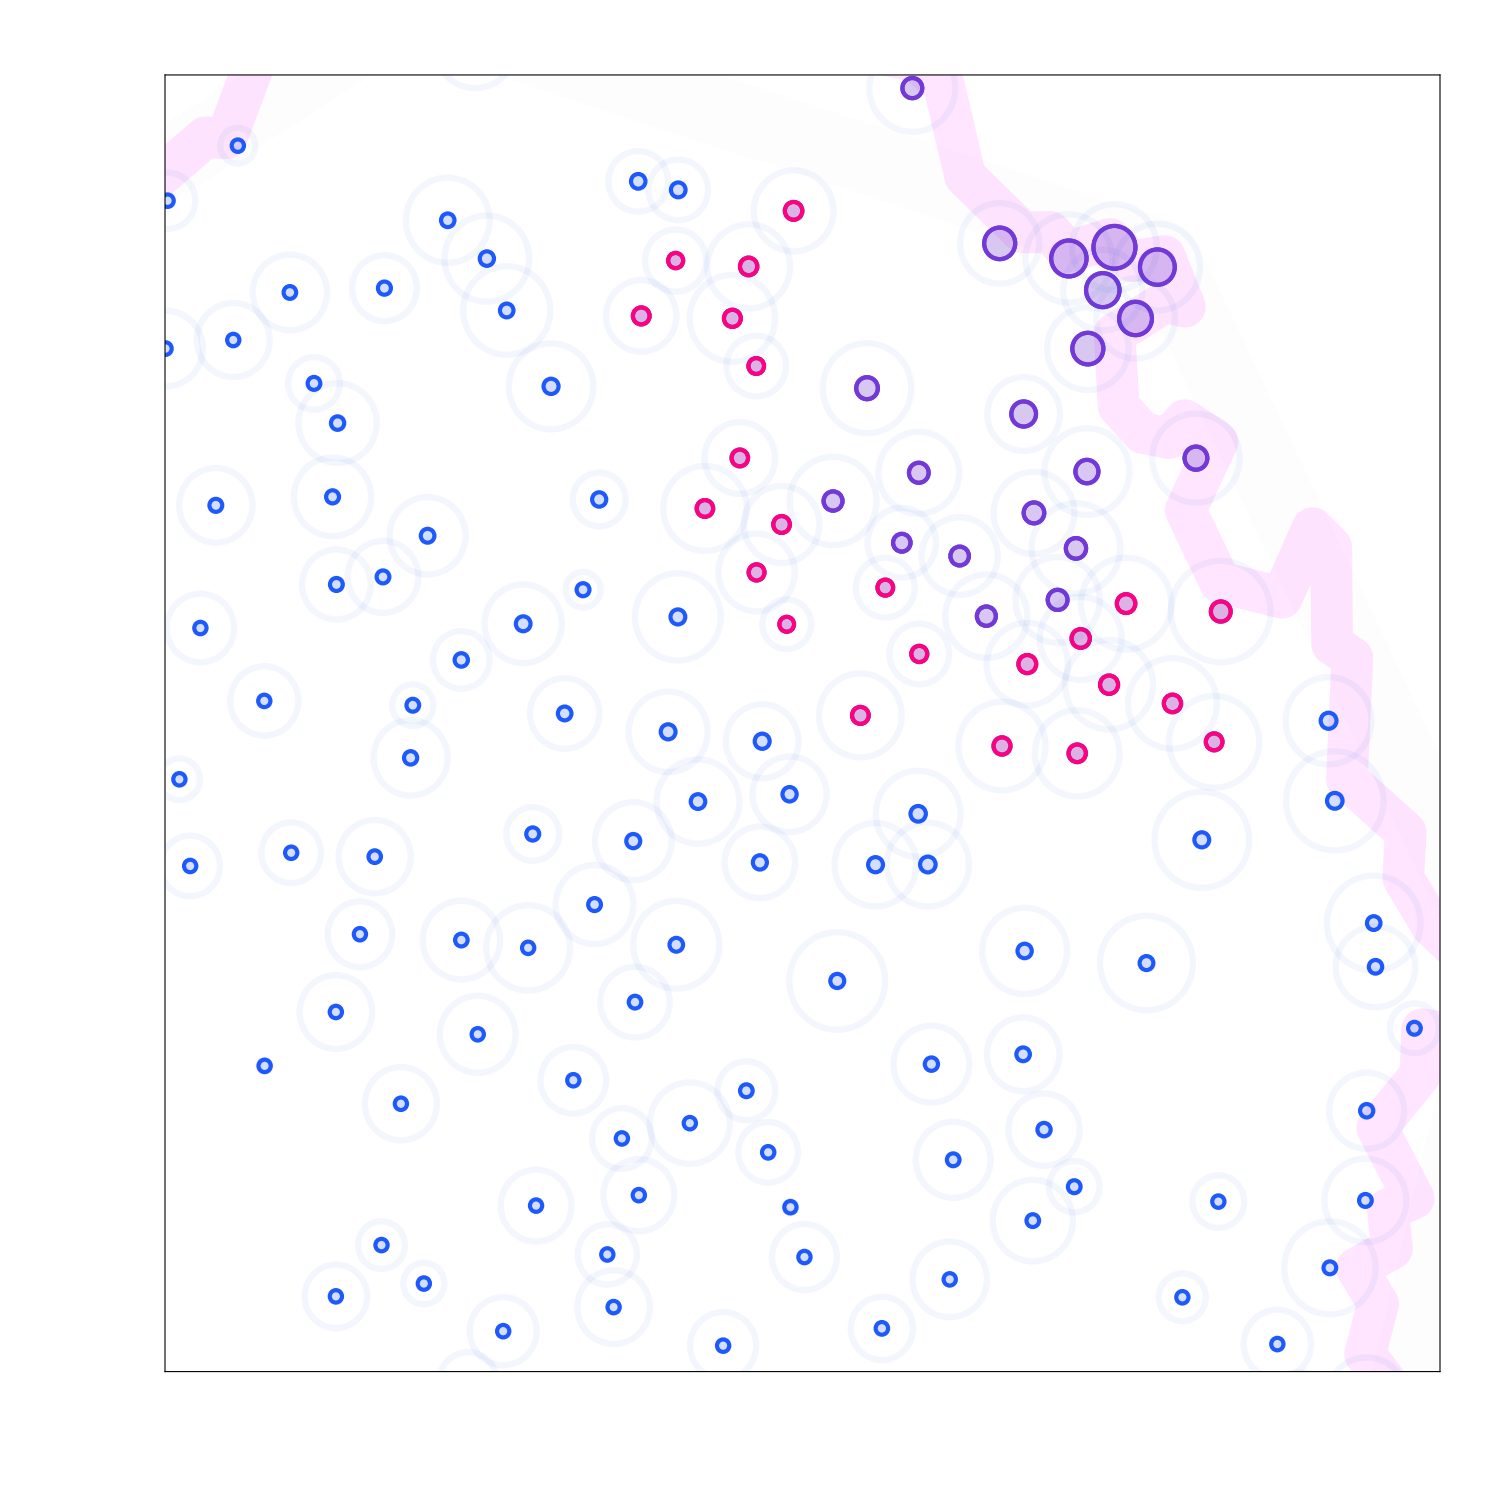

```mathematica
t=100;
freqs=Count[steps[[All,1;;t]]//Flatten,#]&/@Range[1,Length[migration]];
topFreq=(freqs//Sort//Reverse)[[1;;20]];
(*surv=Position[freqs,#]&/@topFreq//Flatten;*)
over=Position[freqs,x_/;1500<x]//Flatten;
surv=Position[freqs,x_/;500<x<1500]//Flatten;
(*Map*)
countryName="São Tomé and Príncipe";
map=MapProcess[freqs, pops, latLon,max,countryName,surv,over];
hst=HistProcess[steps[[All,1;;t]]//Flatten,migration,maxTwo];
surv
out=map(*Grid[{{hst},{map}}];*)
```

## Tests

```mathematica
MatrixPlot[ReplaceDiagonal[migration]
,ColorFunction->Automatic
,ColorFunctionScaling->True
,FrameStyle->Thick
,FrameTicks->None
,ImagePadding->0
];
```